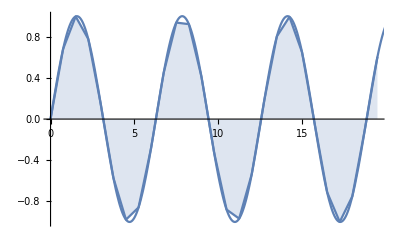

```mathematica
(*
Author: Dawith Lim (cephalopodoverlord@protonmail.com);
Last Modified Date: 2018/03/11;
Description: A sample code of Forward Euler method.
*)

interval = 0.75; (*Currently only works for either integers or finite sums of 1/2^n (positive integer n) *)
maxval=20; (* Needs to be a positive number *)
XValue[0.]=0 ;(* Initializes the first value *)
XFn[n_]:=Sin[XValue[n]]; (* The function *)
X[n_]:=X[n-1]+interval; (* Updates the value of X *)
Show[DiscretePlot[XFn[n],{n,0.,maxval,interval},Joined->True],Plot[Sin[x],{x,0,maxval}]]
```